```mathematica
Poinsot[A_, B_, C0_, r0_, theta0_, b_, alpha_,steps_] :=
 Module[{q0, trif, K2, TP, hP, eq,solP,c,z,X,Y,Z,e},
     q0 = (C0*r0*Tan[theta0])/B;

(*trif = (2*Pi*B)/(r0*(A*Cos[theta0] + C0*Sin[theta0]*Tan[theta0]));*)
     K2 = (B*q0)^2 + (C0*r0)^2;
     TP = 1/2*(B*q0^2 + C0*r0^2);
     hP = Sqrt[(2*TP)/K2];
     eq1P = Derivative[1][p][t] == ((B - C0)*q[t]*r[t])/A;
     eq2P = Derivative[1][q][t] == ((C0 - A)*p[t]*r[t])/B;
     eq3P = Derivative[1][r][t] == ((A - B)*p[t]*q[t])/C0;
     eq4P = Derivative[1][psi][t] ==
       (Cos[phi[t]]*q[t] + p[t]*Sin[phi[t]])/Sin[theta[t]];
     eq5P = Derivative[1][phi][t] ==
       r[t] - Cot[theta[t]]*(Cos[phi[t]]*q[t] + p[t]*Sin[phi[t]]);
     eq6P = Derivative[1][theta][t] == p[t]*Cos[phi[t]] - q[t]*Sin[phi[t]];
     w1P = (Cos[phi[t]]*Cos[psi[t]] - Sin[phi[t]]*Sin[psi[t]]*Cos[theta[t]])*
        p[t] - (Cos[psi[t]]*Sin[phi[t]] +
          Cos[phi[t]]*Cos[theta[t]]*Sin[psi[t]])*q[t] +
       r[t]*Sin[psi[t]]*Sin[theta[t]];
     w2P = (Cos[psi[t]]*Cos[theta[t]]*Sin[phi[t]] + Cos[phi[t]]*Sin[psi[t]])*
        p[t] + (Cos[phi[t]]*Cos[psi[t]]*Cos[theta[t]] -
          Sin[phi[t]]*Sin[psi[t]])*q[t] - Cos[psi[t]]*r[t]*Sin[theta[t]];
     w3P = Cos[theta[t]]*r[t] + Cos[phi[t]]*q[t]*Sin[theta[t]] +
       p[t]*Sin[phi[t]]*Sin[theta[t]];
     solP = NDSolve[{eq1P, eq2P, eq3P, eq4P, eq5P, eq6P, p[0] == 0, q[0] == q0,
        r[0] == r0, psi[0] == 0, phi[0] == 0, theta[0] == theta0},
       {p, q, r, psi, phi, theta}, {t, 0, b},MaxSteps->steps];
     {x, y} = Flatten[{-((w1P*hP)/w3P), -((w2P*hP)/w3P)} /. solP];
     z = x^2 + y^2;
     m = FindMinimum[z, {t, 0.1},AccuracyGoal->3,PrecisionGoal->3];
     M = FindMinimum[-z, {t, 0.1},AccuracyGoal->3,PrecisionGoal->3];
     ra1 = Sqrt[m[[1]]];
     ra2 = Sqrt[-M[[1]]];
     StylePrint["The herpolhode is contained in an annulus having internal radius ra1 and external radius ra2, where","Output",FontFamily->"Times-Plain"];
     Print["ra1 = ", ra1",      ra2 = ",ra2];
     c1 = ParametricPlot[{ra1*Sin[u], ra1*Cos[u]}, {u, 0, 2*Pi},
       AspectRatio -> 1, DisplayFunction -> Identity,
       PlotStyle -> RGBColor[0.8669, 0.258, 0.227]];
     c2 = ParametricPlot[{ra2*Sin[u], ra2*Cos[u]}, {u, 0, 2*Pi},
       AspectRatio -> 1, DisplayFunction -> Identity,
       PlotStyle -> RGBColor[0.925, 0.14, 0.129]];
       StylePrint["The distance ra of the herpolhoid versus time","Output",FontFamily->"Times-Plain"];
       If[A==B||A==C0||B==C0,Goto[1],Goto[2]];
       Label[1];
       Plot[r0,{t, 0, b}, AxesLabel -> {"t","ra"},AxesOrigin->{0,0}]
       Goto[3];
       Label[2];
     Plot[Sqrt[z], {t, 0, b}, AxesLabel -> {"t", "ra"}]
     Label[3];
     erp = ParametricPlot[{x, y}, {t, 0, b}, AspectRatio -> 1,
       PlotRange -> All, DisplayFunction -> Identity];
       StylePrint["Herpolhode","Output",FontFamily->"Times-Plain"];
     Label[3]; xp = p[t]/Sqrt[2*TP] /. solP;
     yp = q[t]/Sqrt[2*TP] /. solP;
     zp = r[t]/Sqrt[2*TP] /. solP;
     X = (Cos[u]*Sin[v])/Sqrt[A];
     Y = (Sin[u]*Sin[v])/Sqrt[B];
     Z = Cos[v]/Sqrt[C0];
     el =
      ParametricPlot3D[{X, Y, Z}, {u, 0, 2*Pi}, {v, 0, alpha},
       Lighting -> Automatic, Boxed -> False,
       DisplayFunction -> Identity];
     pol = ParametricPlot3D[Evaluate[Flatten[{xp, yp, zp}] /. solP],
       {t, 0, b}, PlotPoints -> 200, DisplayFunction -> Identity];
       StylePrint["The polhode on the ellipsoid of inertia","Output",
      FontFamily->"Times-Plain"];
Show[erp, c1, c2, DisplayFunction -> $DisplayFunction]
     Show[el, pol, DisplayFunction -> $DisplayFunction]
]
```

The herpolhode is contained in an annulus having internal radius ra1 and external radius ra2, where

ra1 = 0.032037 ,      ra2 = 0.483046

The distance ra of the herpolhoid versus time

Herpolhode

The polhode on the ellipsoid of inertia

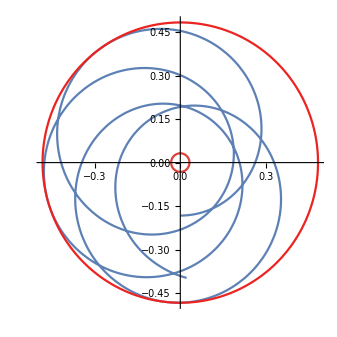
-Graphics- -Graphics3D-

```mathematica
A=0.5;
B=1;
C0=1.5;
r0=3;
θ0=π/4;
T=3;
α=π/2;
steps=1000;
Poinsot[A, B, C0, r0, θ0, T, α,steps]
```

```mathematica
A=1;
B=1;
C0=0.5;
r0=3;
θ0=π/4;
T=3;
α=π/2;
Poinsot[A, B, C0, r0, θ0, T, α,1000]
```

The herpolhode is contained in an annulus having internal radius ra1 and external radius ra2, where

ra1 = 0.408248 ,      ra2 = 0.408248

The polhode on the ellipsoid of inertia

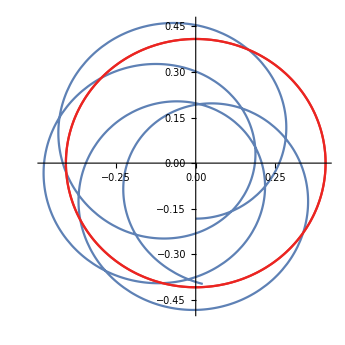
-Graphics- -Graphics3D-

```mathematica
"The distance ra of the herpolhoid versus time"s
```

The herpolhode is contained in an annulus having internal radius ra1 and external radius ra2, where

ra1 = 0.00239699 ,      ra2 = 0.0407696

The distance ra of the herpolhoid versus time

Herpolhode

The polhode on the ellipsoid of inertia

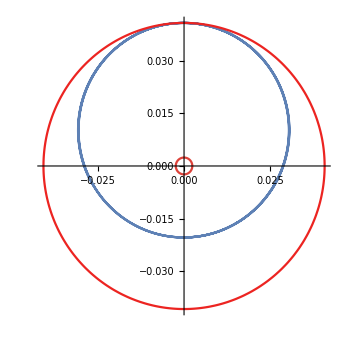
-Graphics- -Graphics3D-

```mathematica
A=0.5;
B=1;
C0=1.5;
r0=3;
θ0=0.05;
T=4;
α=π/20;
Poinsot[A, B, C0, r0, θ0, T, α,1000]
```

The herpolhode is contained in an annulus having internal radius ra1 and external radius ra2, where

ra1 = 0.0333895 ,      ra2 = 0.0333895

The distance ra of the herpolhoid versus time

Herpolhode

The polhode on the ellipsoid of inertia

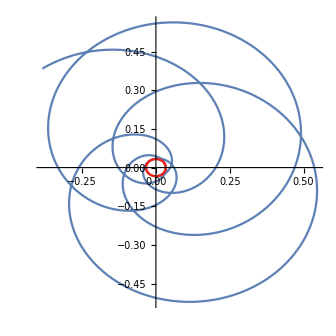
-Graphics- -Graphics3D-

```mathematica
A=0.5;
B=1.5;
C0=1;
r0=1;
θ0=-0.1;
T=30;
α=π;
Poinsot[A, B, C0, r0, θ0, T, α,1000]
```